```mathematica
Get[NotebookDirectory[]<>#]&/@{
"23_10_04_parameters_1.m",
"23_10_04_simulation_1.m",
"23_10_04_styles_1.m"
};
```

```mathematica
(*fix parvals*)
Clear[FinalStates];
FinalStates[pars_,environment_,fluxvars_,inivalues_]:=FinalStates[pars,environment,fluxvars,inivalues]=Module[{sol},
sol=simulate[pars/.environment,environment,fluxvars,inivalues/.pars];
Table[state->(state[tmax/.pars]/.sol),{state,states}]
];
```

```mathematica
(*add units to final state plots!*)
```

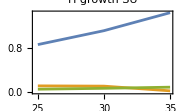

```mathematica
FinalStatePlotLabel={w->"°C",Ν->"DIN: μmol N L^-1",X->"Prey: C-μmol X L^-1",L->"Light: mol photos m^-2 d^-1"};
Clear[FinalStatePlot];
FinalStatePlot[parvals_,environment_,toplotys_,parameter_,parameterrange_,inivals_,legend_,plotrange_,options_,parxAxisMult_]:=Module[{list=Table[
Table[Module[{
parvals2,
environment2
},

{parvals2,environment2}={parvals,environment}/.((parameter->_)->(parameter->value));
;{parxAxisMult value,Evaluate[toploty//.(rulesnofluxvars)/.parvals2/.FinalStates[parvals2,environment2,fluxvars,inivals]/.environment2/.t->(tmax/.parvals2)]}],{value,parameterrange}],{toploty,toplotys}]},
ListPlot[list,Evaluate@options,PlotRange->(toplotys[[1]]/.plotrange),Joined->True,AxesOrigin->Automatic,ImageSize->Small,PlotStyle->If[Length@list==3,({#,AbsoluteThickness[2]}&/@(ColorData[97]/@Range[3])),{Darker@Brown,AbsoluteThickness[2]}],LabelStyle->{FontFamily->fontfamily,FontSize->12}(*,ImagePadding->{{30,45},{32,5}}*),(*AxesLabel->{parameter/.FinalStatePlotLabel},*)PlotLegends->legend,PlotRange->Full,PlotRangeClipping->None,ClippingStyle->Automatic,PlotLabel->eqstyle[toplotys[[1]]/.Piecewise[{{names, Length[toplotys]==1}, {SUnames, True}}]],FrameLabel->{{unitstyle[toplotys[[1]]/.Piecewise[{{units, Length[toplotys]==1}, {SUunits, True}}]],None},{unitstyle[parameter/.FinalStatePlotLabel],None}},(*ImagePadding->{{55,100},{35,5}},*)Evaluate@timeplotstyle]
];
ticksmanual[min_,max_]:=N@FindDivisions[{0,max},3];
FinalStatePlot[parvalsFvFmArr,{w->w0},toplotSUs[[1]],w,Range[w0-3,w0+7,5],inivalsdefault,{"a","b","c"},_->Full,{},1]
```

```mathematica
wmin=20;wmax=40;
rangewFinalStatePlot=Range[wmin,wmax,.5];
yranges=({jHGm->{0,jHGmmax},jSGm->{0,jSGmmax}, jCPm->{0,jCPmmax},_->Full}/.SUmaxs);
finalplot[filename_,parvals_,environment_,parameter_,parameterrange_,inivals_,yranges_,arrangement_,optionss_,parxAxisMult_]:=(Export[NotebookDirectory[]<>"export/"<>filename,#];#)&@Style[arrangement@Join[Insert[Table[
FinalStatePlot[parvals,environment,{x},parameter,parameterrange,inivals,None,{_->Full},x/.optionss,parxAxisMult]
,{x,toplot}],Nothing,-3],
Table[
FinalStatePlot[parvals,environment,SUins,parameter,parameterrange,inivals,({SUins[[1]],Piecewise[{{Column[{"effective","light"},Alignment->Center], SUins[[1]]==jCPm}, {"C", True}}],Piecewise[{{"CO_2", SUins[[1]]==jCPm}, {"N", True}}]}/.AlternativeNamesforSU/.names),yranges,x/.optionss,parxAxisMult]
,{SUins,toplotSUs}]],LineBreakWithin->False];
finalplotoptionss={_->{Ticks->{Range[wmin+1,wmax,2],ticksmanual},AxesOrigin->{Automatic,0}}};
```

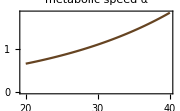
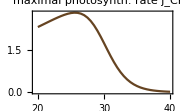
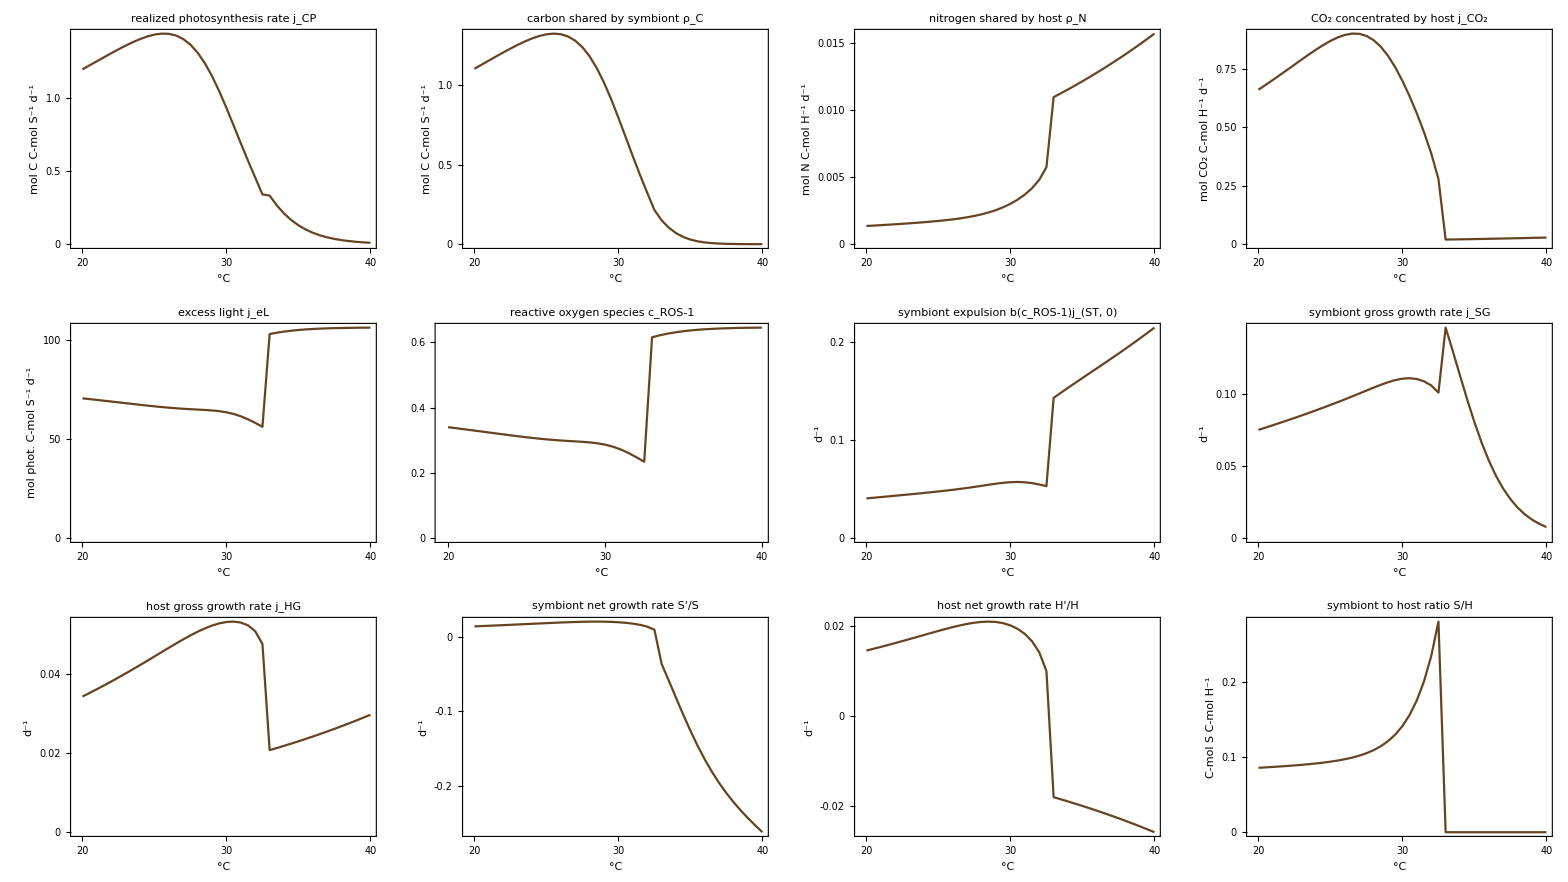
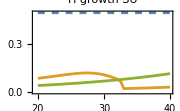
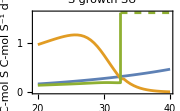
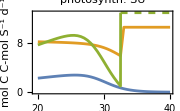
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
arrangementFinalStatePlot=Column[{Framed[Row[#1⟦{1,2}⟧],RoundingRadius->framingRadius],arrow1,Framed[Column[{Multicolumn[#1⟦3;;-4⟧,4,Appearance->"Horizontal",Alignment->Center],Row[#1⟦-3;;-1⟧]}],RoundingRadius->framingRadius]},Alignment->Center,Spacings->0]&;
finalplot["steadystate-FvFm-Arr.pdf",parvalsFvFmArr,{w->"doesn't matter"},w,rangewFinalStatePlot,inivalsdefault,yranges,arrangementFinalStatePlot,finalplotoptionss,1]
```

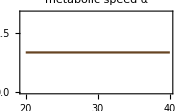
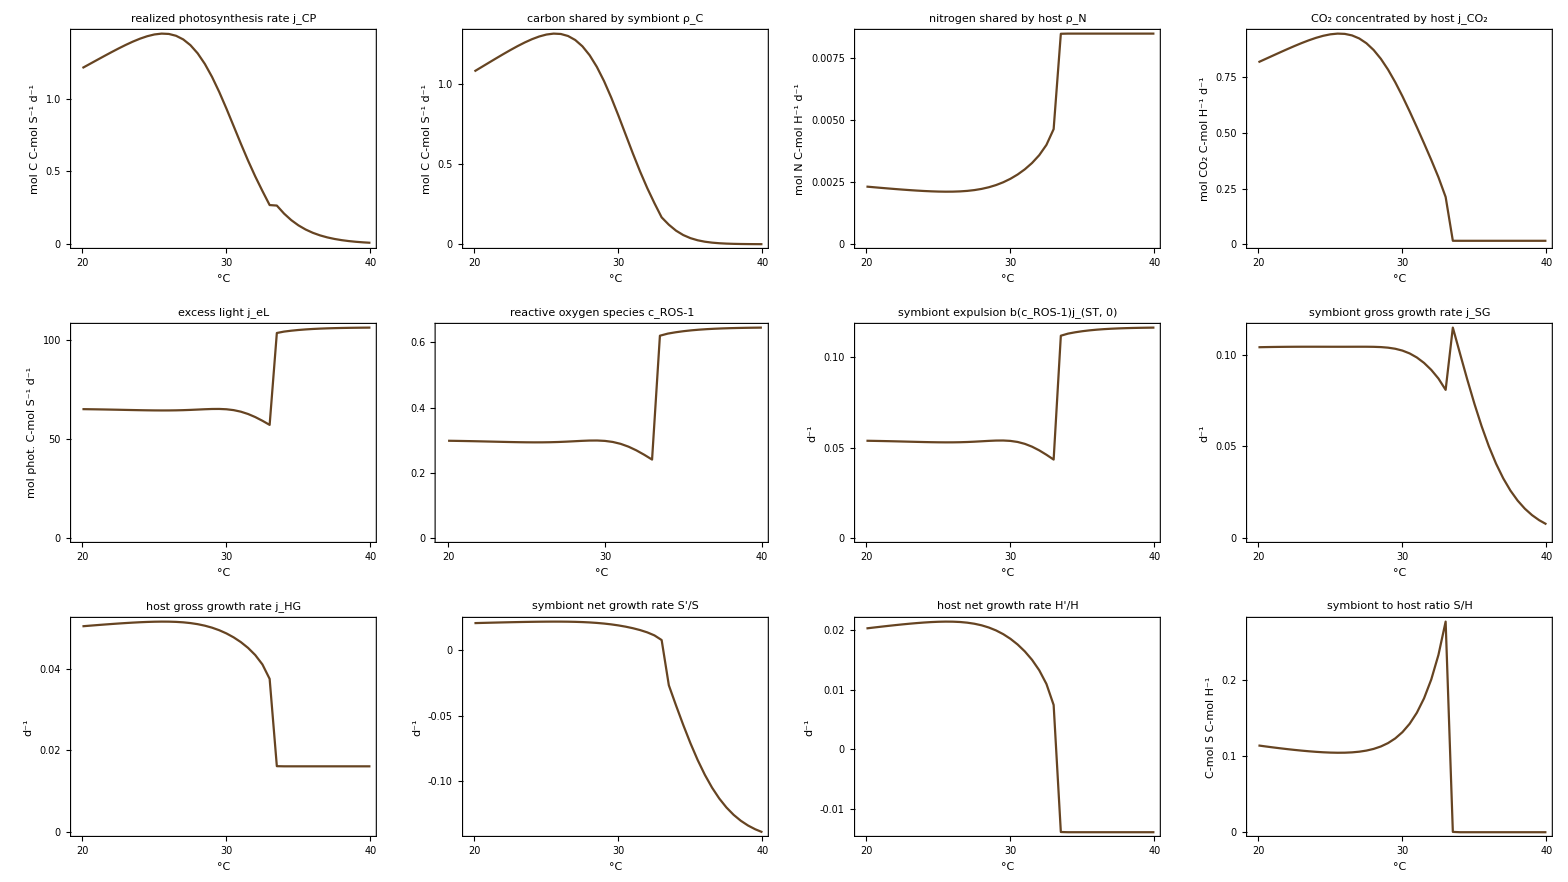
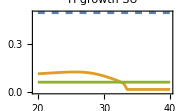
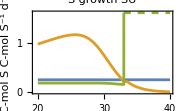
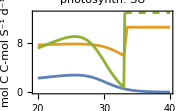
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
finalplot["steadystate-FvFm.pdf",parvalsFvFm,{w->"doesn't matter"},w,rangewFinalStatePlot,inivalsdefault,yranges,arrangementFinalStatePlot,finalplotoptionss,1]
```

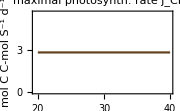
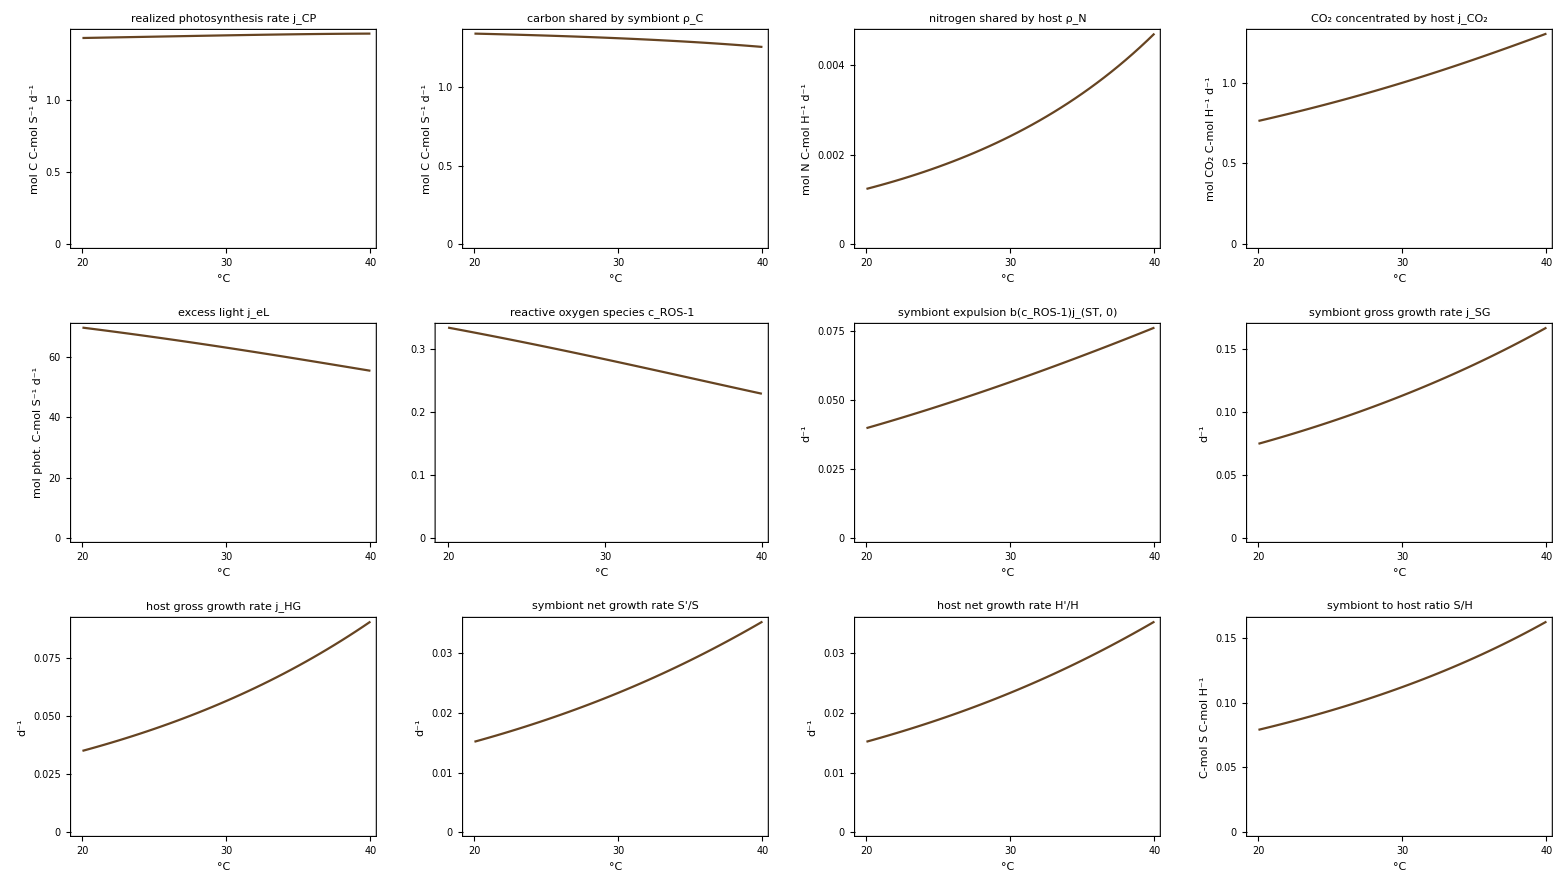
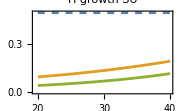
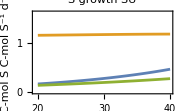
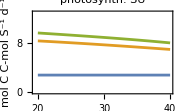
-Graphics--Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
finalplot["steadystate-Arr.pdf",parvalsArr,{w->"doesn't matter"},w,rangewFinalStatePlot,inivalsdefault,Join[{jCP->{0,1.2}},yranges],arrangementFinalStatePlot,finalplotoptionss,1]
```

```mathematica
(*fix axes in 2D plots*)
```

```mathematica
arrangementFinalStatePlotN=Framed[Column[{Multicolumn[#1⟦3;;-4⟧,4,Appearance->"Horizontal"],Row[#1⟦-3;;-1⟧]},Alignment->Center],RoundingRadius->framingRadius]&;
```

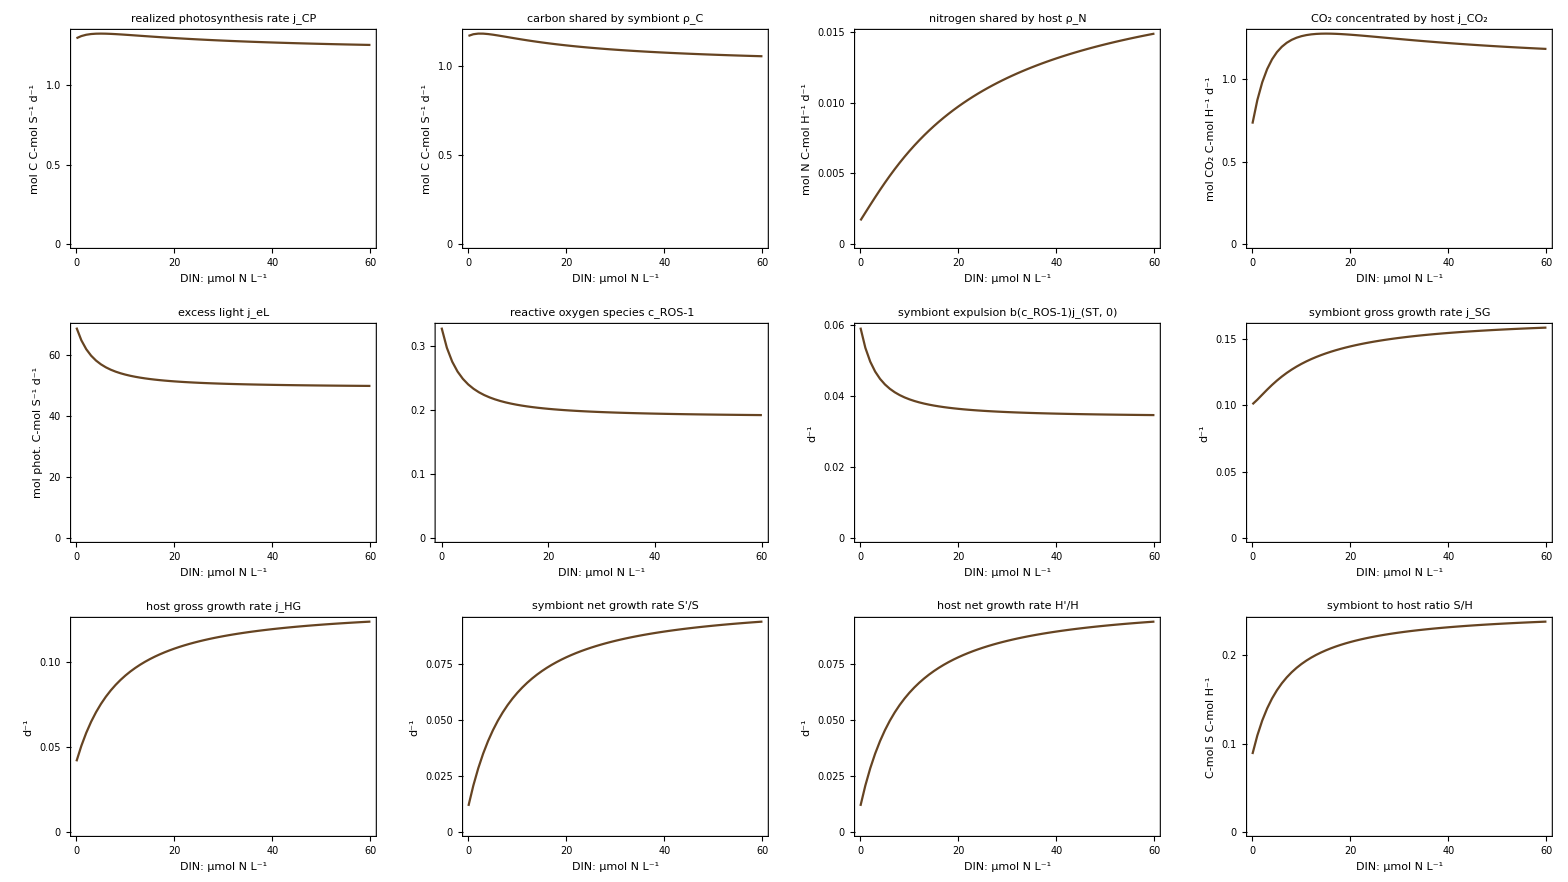
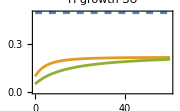
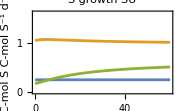
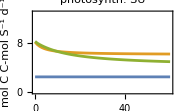

```mathematica
rangeΝFinalStatePlot=Range[0, 6 10^-6.,.1 10^-6.];
finalΝoptions={_->{AxesOrigin->{0,0},Ticks->{ticksmanual,ticksmanual},ImagePadding->{{55,25},{40,5}}}};
finalplot["steadystate-FvFm-Arr-N-high-jHGm.pdf",parvalsFvFmArr(*/.((L->_)->(L->40))*),{w->28},Ν,rangeΝFinalStatePlot,inivalsdefault,yranges,arrangementFinalStatePlotN,finalΝoptions,10^7]
```

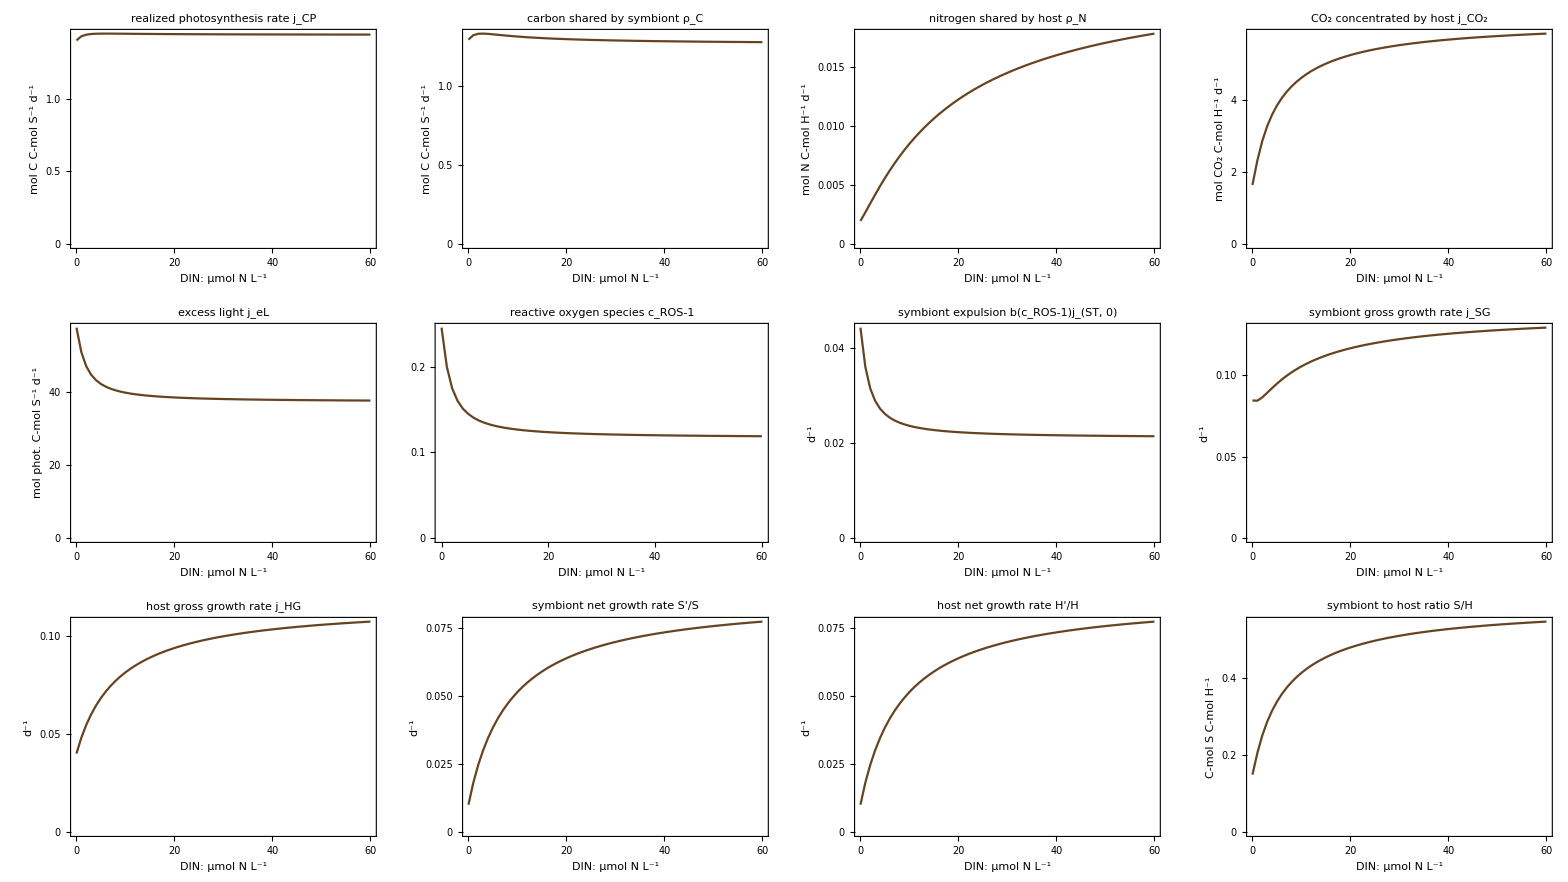
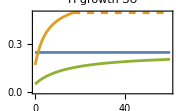
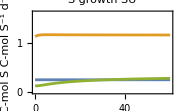
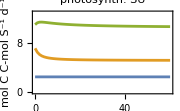

```mathematica
finalplot["steadystate-FvFm-Arr-N-low-jHGm.pdf",parvalsFvFmArr/.{(jHGm->_)->(jHGm->.25)},{w->28},Ν,rangeΝFinalStatePlot,inivalsdefault,yranges,arrangementFinalStatePlotN,finalΝoptions,10^7]
```

```mathematica
bleachedSH=0.02;
ConditionsAndColors={
{S/H>bleachedSH∧jHG-jHT>0∧jSG-jST>0,ColorData[97][15],"not bleached, growing coral"},
{S/H<bleachedSH∧jHG-jHT<0,ColorData[97][4],"bleached, dying coral"},
{jHG-jHT<0,ColorData[97][5],"not bleached, dying coral"},
{True,ColorData[97][8],"bleached, growing coral"}
};
```

```mathematica
ConditionsAndColors2={
{S/H>bleachedSH∧jHG-jHT>0∧jSG-jST>0,ColorData[97][15],Column[{"not bleached, growing coral"},Alignment->Center]},
{True,ColorData[97][4],Column[{"bleached and/or dying coral"},Alignment->Center]}
};
legendFinalState2DDiscretePlot[ConditionsAndColors_]:=Framed[SwatchLegend[ConditionsAndColors[[All,2]],ConditionsAndColors[[All,3]](*,LegendLayout->"Grid"*)(*,LabelStyle->{FontFamily->fontfamily}*)],RoundingRadius->10];
legendFinalState2DDiscretePlot[ConditionsAndColors2]
```

```mathematica
FinalState2DDiscretePlot[parvals_,inivals_,ConditionsAndColors_,parY_,rangew_,rangeY_,contours_,parYAxisMult_,ticknumberaimw_,ticknumberaimY_,legend_,epilog_,names_]:=Module[{
list,ticksw,ticksY
},
list=Table[
Module[{parameters,environment,changeX,changeY},

parameters=parvals/.((parY->_)->(parY->valY));
environment={w->valw};

list=Evaluate@Piecewise[Table[
{
 i,
ConditionsAndColors[[i,1]]//.(rulesnofluxvars)/.parameters/.FinalStates[parameters,environment,fluxvars,inivalsdefault]/.environment/.t->(tmax/.parameters)},{i,Length@ConditionsAndColors}]]
],
{valw,rangew},
{valY,rangeY}
];
Grid[{{
ticksw=Table[{i,N@rangew[[i]] },{i,1,Length@rangew,Round[Length@rangew/ticknumberaimw]}];
ticksY=Table[{i,parYAxisMult N@rangeY[[i]]},{i,1,Length@rangeY,Round[Length@rangeY/ticknumberaimY]}];
ArrayPlot[list,Ticks->None,ColorFunctionScaling->False,ColorFunction->Function[arg,Piecewise[Table[{ConditionsAndColors[[i,2]],arg==i},{i,Length@ConditionsAndColors}]]],FrameTicks->{ticksw,ticksY},FrameLabel->(eqstyle/@({"°C",parY}/.names)),DataReversed->True,Frame->True,Mesh->False(*True*)(*,MeshStyle->{{Black,Opacity[.25]}}*),ImageSize->220,ImagePadding->{{75,5},{50,5}},LabelStyle->12,Epilog->epilog],
Column[{Spacer[{0,20}],If[legend,legendFinalState2DDiscretePlot[ConditionsAndColors],Nothing]}]
}},Alignment->Top]
];
(*legendFinalState2DDiscretePlot[ConditionsAndColors]*)
(*legendFinalState2DDiscretePlot[ConditionsAndColors2]*)
```

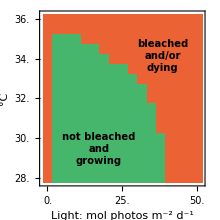
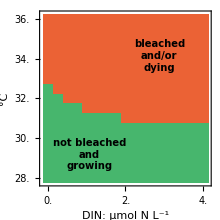
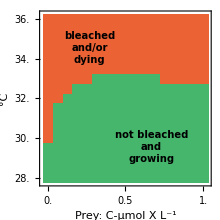
-Graphics- | -Graphics- | -Graphics- |

```mathematica
steps=16(*40*);
minTemp=28;
maxTemp=36;
rangeTemp=Range[minTemp,maxTemp,(maxTemp-minTemp)/steps];
maxL=5 10;
rangeL=Range[0,maxL,maxL/steps];
maxN=   4 10^-6 ;
maxX=1 10^-6;
rangeN=Range[0,maxN,  maxN/steps];
rangeX=Range[0,maxX,  maxX/steps];
ConditionsAndColors2Light={#[[1]],Lighter@#[[2]],#[[3]]}&/@ConditionsAndColors2;
epilogstyle={10,Bold};
names2DLong=FinalStatePlotLabel;
multiplier2D={L->1,Ν->10^6,X->10^6};
label1=Column[{"not bleached","and","growing"},Alignment->Center];
label2=Column[{"bleached","and/or","dying"},Alignment->Center];
epilogReplace2D={
L->{{label1,{15 #,8.5 #}},{label2,{32#,32#}}},
Ν->{{label1,{12#,7#}},{label2,{30#,32#}}},
X->{{label1,{28#,9#}},{label2,{12#,34#}}}
}&@(steps/40);
rangeReplace2D={L->rangeL,Ν->rangeN,X->rangeX};
tmaxFinalContourPlot=1500;
(*With[{x=Ν},FinalState2DDiscretePlot[parvalsFvFmArr,inivalsdefault,ConditionsAndColors2,x,rangeTemp,x/.rangeReplace2D,Automatic,x/.multiplier2D,4,4,False,Table[Inset[Style[epi[[1]],epilogstyle],epi[[2]]],{epi,x/.epilogReplace2D}],names2DLong]]*)
(*to do: add individual labels, redo N and X, export, copy in Overleaf*)
FinalState2DRow[ConditionsAndColors_,parvals_,epilogReplace_,names_]:=
Table[FinalState2DDiscretePlot[parvals,inivalsdefault,ConditionsAndColors,x,rangeTemp,x/.rangeReplace2D,Automatic,x/.multiplier2D,4,4,False,Table[Inset[Style[epi[[1]],epilogstyle],epi[[2]]],{epi,x/.epilogReplace}],names],{x,{L,Ν,X}}];
(Export[NotebookDirectory[]<>"/export/2Dplot-maintext.pdf",#];#)&@Row@FinalState2DRow[ConditionsAndColors2,Join[{tmax->tmaxFinalContourPlot},parvalsFvFmArr],epilogReplace2D,names2DLong]
```

```mathematica
FinalState2DDiscretePlot[ConditionsAndColors_,parvals_]:=
Join[{
legendFinalState2DDiscretePlot[ConditionsAndColors]},FinalState2DRow[ConditionsAndColors,parvals,{_->{}},names2DLong]];
```

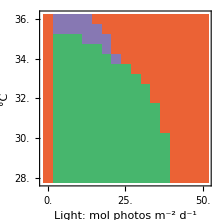
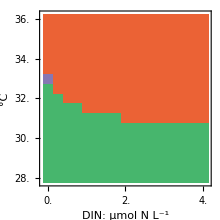
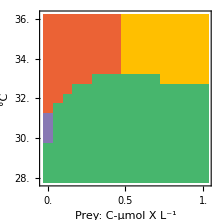
-Graphics- | -Graphics- | -Graphics- |

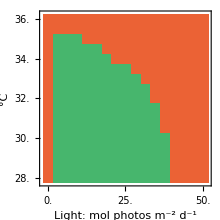
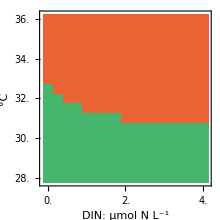
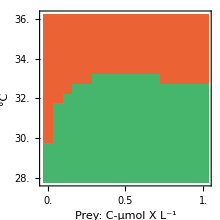
-Graphics- | -Graphics- | -Graphics- |

```mathematica
FinalState2DDiscretePlotExport[filename_,ConditionsAndColors_,parvals_]:=
(Export[NotebookDirectory[]<>"/export/"<>filename,#];#)&@Column[{#[[1]],Row[#[[2;;-1]]]}&@FinalState2DDiscretePlot[ConditionsAndColors,parvals],Alignment->Center];
FinalState2DDiscretePlotExport["2Dplot4-FvFm-Arr.pdf",ConditionsAndColors,Join[{tmax->tmaxFinalContourPlot},parvalsFvFmArr]]
FinalState2DDiscretePlotExport["2Dplot2-FvFm-Arr.pdf",ConditionsAndColors2,Join[{tmax->tmaxFinalContourPlot},parvalsFvFmArr]]
```

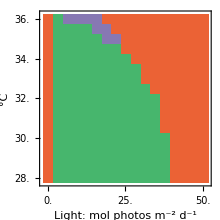
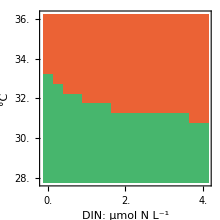
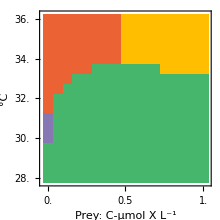
-Graphics- | -Graphics- | -Graphics- |

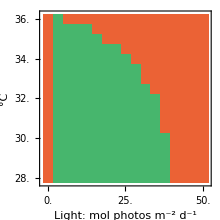
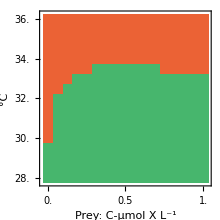
-Graphics- | -Graphics- | -Graphics- |

```mathematica
FinalState2DDiscretePlotExport["2Dplot4-FvFm.pdf",ConditionsAndColors,Join[{tmax->tmaxFinalContourPlot},parvalsFvFm]]
FinalState2DDiscretePlotExport["2Dplot2-FvFm.pdf",ConditionsAndColors2,Join[{tmax->tmaxFinalContourPlot},parvalsFvFm]]
```

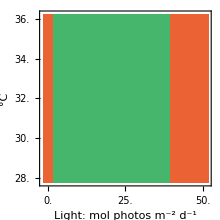
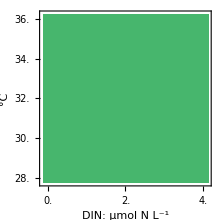
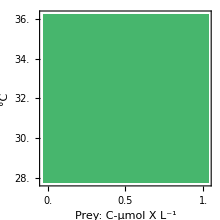
-Graphics- | -Graphics- | -Graphics- |

-Graphics- | -Graphics- | -Graphics- |

```mathematica
FinalState2DDiscretePlotExport["2Dplot4-Arr.pdf",ConditionsAndColors,parvalsArr]
FinalState2DDiscretePlotExport["2Dplot2-Arr.pdf",ConditionsAndColors2,parvalsArr]
```

```mathematica
(*FinalState2DDiscretePlotExport["2Dplot4-FvFm-Arr-low-jHGm.pdf",ConditionsAndColors,Join[{tmax->tmaxFinalContourPlot},parvalsFvFmArr/.{(jHGm->_)->(jHGm->.25)}]]
FinalState2DDiscretePlotExport["2Dplot2-FvFm-Arr-low-jHGm.pdf",ConditionsAndColors2,Join[{tmax->tmaxFinalContourPlot},parvalsFvFmArr/.{(jHGm->_)->(jHGm->.25)}]]*)
```